## Plotting

Expressions defining functions in one variable can be plotted:

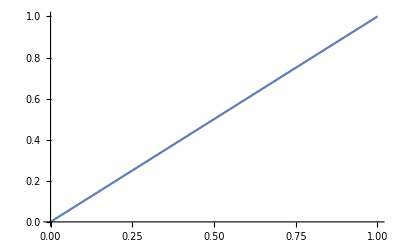

```mathematica
Plot[x,{x,0,1}]
```

The syntax {x,0,1} defines a list (similar to an array in Julia).
Lists can contain anything, and can be arbitrarily nested

```mathematica
{x,0,1}
```

{x,0,1}

We will see later how to access and manipulate lists. For now we will just use simple lists to define the axes.

## More plotting

The plotting and visualization functionality of Mathematica is very advanced
You can read the built-in documentation to learn more
Some examples:

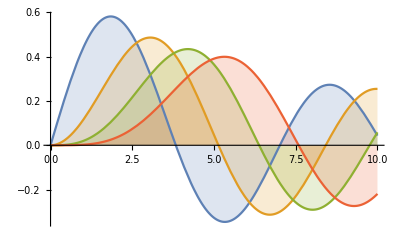

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

## Interactivity

One of Mathematica’s most powerful features is its interactivity

Consider plotting a set of parabolas

y=(x-a)^2

parameterized by the value a

We begin by choosing a “representative” set

```mathematica
parabolas=Table[(x-a)^2,{a,-2,2,1/2}]
```

{(2+x)^2,(3/2+x)^2,(1+x)^2,(1/2+x)^2,x^2,(-1/2+x)^2,(-1+x)^2,(-3/2+x)^2,(-2+x)^2}

Plotting these functions gives us some insight

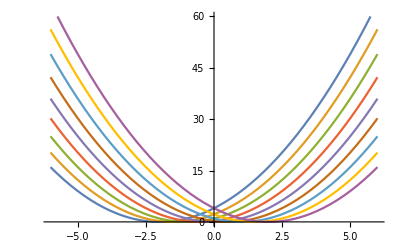

```mathematica
Plot[parabolas,{x,-6,6},PlotRange->{0,60}]
```

More useful is manipulating the parameter interactively

```mathematica
Manipulate[Plot[(x-a)^2,{x,-6,6},PlotRange->{0,60}],{a,-2,2}]
```

We can use manipulate to understand e.g. frequency and amplitude of waves

```mathematica
Manipulate[
Plot[a*Sin[ω*x],{x,0,2π},PlotRange->{-3,3}],
{a,1,3},
{ω,1,10}
]
```